### Start choosing the example:

```mathematica
t=18;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Get::noopen: Cannot open /Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m.

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
(crit=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->1,U1->0,S1->0,S2->0}]])//AbsoluteTiming
```

{1-u1+u2==0&&1-u2==0,u1≤u1,True}

{0.068495,<|j8→1,j7→0,j5→0,j2→1,j1→0,j4→1,j3→0,j6→1,u6→0,jt1→0,jt2→1,jt3→1,jt4→0,jt5→1,jt6→0,u5→0,u8→2,u3→1,u4→0,u7→2,u1→2,u2→1|>}

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->0,S1->0,S2->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
True
and the rules are:
<|j580→1,u597→0,j577→1,j578→1,j579→1,j581→0,j582→0,j583→0,j584→0,jt585→0,jt586→1,jt587→1,jt588→0,jt589→1,jt590→0,u593→0,u595→-1+2,u596→-1+1,u598→2,u591→2,u592→1,u594→2|>

DataToEquations: The system is:
True
and the rules are:
<|j580→1,u597→0,j577→1,j578→1,j579→1,j581→0,j582→0,j583→0,j584→0,jt585→0,jt586→1,jt587→1,jt588→0,jt589→1,jt590→0,u593→0,u595→-1+2,u596→-1+1,u598→2,u591→2,u592→1,u594→2|>

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.009585,Null}

<|{1,1->2}→2,{1,en575->1}→2,{2,1->2}→1,{2,2->3}→1,{3,2->3}→0,{3,3->ex576}→0,{en575,en575->1}→2,{ex576,3->ex576}→0|>

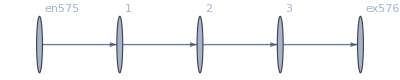

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]](*//KeySort*)
```

<|j543→1,j544→0,u572→0,j539→1,j540→1,j541→0,j542→1,j545→0,j546→0,j547→0,j548→0,j549→0,j550→0,jt551→0,jt552→1,jt554→0,jt555→0,jt556→0,jt557→0,jt558→0,jt559→1,jt560→0,jt561→0,jt562→0,u566→0,u569→1,u570→0,u571→1,u573→2,u574→u568,u564→1,u567→2,jt553→1,u563→2,u565→1|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j577→1,j578→1,j579→1,j580→1,j581→0,j582→0,j583→0,j584→0,jt585→0,jt586→1,jt587→1,jt588→0,jt589→1,jt590→0,u591→1.41151,u592→0.705756,u593→0,u594→1.41151,u595→0.705756,u596→0,u597→0,u598→1.41151|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```